## Define Large N Matrix Elements

These follow from Appendix C

### LCT Basis

```mathematica
LargeNLCT[m_,n_]:=If[EvenQ[m+n],2 √((2m+1)(2n+1)) (HarmonicNumber[1/2 (-1+kM)]+HarmonicNumber[kM/2]-HarmonicNumber[1/2 (-1-km+kM)]-HarmonicNumber[(km+kM)/2])/.{km->Min[m,n],kM->Max[m,n]},0];
```

### Cosine Basis

```mathematica
LargeNCos[m_,n_]:=1/2 If[m==n,4 (-1+(-1)^n-EulerGamma+2 CosIntegral[n π]-CosIntegral[2 n π]+Log[2/(n π)]+n π SinIntegral[n π]),1/((m-n) (m+n))2 (1+(-1)^(m+n)) (2 m^2 CosIntegral[m π]+(-m^2+n^2) CosIntegral[(m-n) π]+n^2 (-2 CosIntegral[n π]+CosIntegral[(m+n) π]-Log[-1+m^2/n^2])+m^2 (-CosIntegral[(m+n) π]+Log[1-n^2/m^2]))];
LargeNCos[0,n_]:=0;
LargeNCos[n_,0]:=0;
LargeNCos[0,0]:=0;
```

### Sine Basis (Note: wrong boundary conditions, so convergence will be extremely slow)

We don’t use these matrix elements, but present them for completeness if the user wants to see the comparison to the other bases.

```mathematica
LargeNSine[m_,n_]:=1/2 If[m==n,4 (-1+(-1)^n-EulerGamma+CosIntegral[2 n π]-Log[2 n π]+n π SinIntegral[n π]),-1/((m-n) (m+n))2 (1+(-1)^(m+n)) (-2 m n CosIntegral[m π]+(m-n) (m+n) CosIntegral[(m-n) π]+2 m n CosIntegral[n π]-m^2 CosIntegral[(m+n) π]+n^2 CosIntegral[(m+n) π]+2 m n Log[m]-m^2 Log[m-n]+n^2 Log[m-n]-2 m n Log[n]+(m-n) (m+n) Log[m+n])];
LargeNSine[0,n_]:=0;
LargeNSine[n_,0]:=0;
LargeNSine[0,0]:=0;
```

## Making Figure 8

Tabulate the matrix elements for just the odd sector cosine and LCT

```mathematica
precision=40;
```

```mathematica
Monitor[matrixCos=Table[N[LargeNCos[m,n],precision],{m,1,300,2},{n,1,300,2}];,{m,n}]//AbsoluteTiming
```

{10.1688,Null}

Using the cosine basis, this is what the odd sector Hamiltonian looks like for the first 10 states:

```mathematica
matrixCos[[1;;10,1;;10]]//Chop//N//MatrixForm
```

(5.91826 | -0.716561 | -0.327885 | -0.192518 | -0.128209 | -0.0922066 | -0.0698578 | -0.0549574 | -0.0444875 | -0.0368284
-0.716561 | 23.3617 | -1.99281 | -1.15375 | -0.777655 | -0.567855 | -0.436437 | -0.347757 | -0.284679 | -0.238
-0.327885 | -1.99281 | 42.0739 | -2.7828 | -1.77444 | -1.27779 | -0.979905 | -0.782312 | -0.642655 | -0.539448
-0.192518 | -1.15375 | -2.7828 | 61.1389 | -3.35076 | -2.25576 | -1.68984 | -1.3364 | -1.09382 | -0.917316
-0.128209 | -0.777655 | -1.77444 | -3.35076 | 80.3751 | -3.7936 | -2.64635 | -2.03603 | -1.64501 | -1.37053
-0.0922066 | -0.567855 | -1.27779 | -2.25576 | -3.7936 | 99.7127 | -4.15637 | -2.97429 | -2.33325 | -1.91531
-0.0698578 | -0.436437 | -0.979905 | -1.68984 | -2.64635 | -4.15637 | 119.118 | -4.46354 | -3.25663 | -2.59314
-0.0549574 | -0.347757 | -0.782312 | -1.3364 | -2.03603 | -2.97429 | -4.46354 | 138.571 | -4.72987 | -3.50437
-0.0444875 | -0.284679 | -0.642655 | -1.09382 | -1.64501 | -2.33325 | -3.25663 | -4.72987 | 158.059 | -4.96493
-0.0368284 | -0.238 | -0.539448 | -0.917316 | -1.37053 | -1.91531 | -2.59314 | -3.50437 | -4.96493 | 177.576)

```mathematica
Monitor[matrixLCT=Table[N[LargeNLCT[m,n],precision],{m,1,300,2},{n,1,300,2}];,{m,n}]//AbsoluteTiming
```

{4.91819,Null}

This is what the LCT odd sector Hamiltonian looks like for the first 10 states

```mathematica
(matrixLCT//N)[[1;;10,1;;10]]//MatrixForm
```

(6. | 1.52753 | 0.765942 | 0.479157 | 0.335548 | 0.251716 | 0.197802 | 0.160728 | 0.133947 | 0.11386
1.52753 | 25.6667 | 8.48247 | 4.83071 | 3.25841 | 2.39856 | 1.86439 | 1.50457 | 1.24811 | 1.05749
0.765942 | 8.48247 | 50.2333 | 18.9008 | 11.5196 | 8.11939 | 6.16684 | 4.90782 | 4.03441 | 3.39687
0.479157 | 4.83071 | 18.9008 | 77.7857 | 31.7407 | 20.2132 | 14.6762 | 11.3943 | 9.22432 | 7.68773
0.335548 | 3.25841 | 11.5196 | 31.7407 | 107.501 | 46.441 | 30.519 | 22.6472 | 17.8755 | 14.6622
0.251716 | 2.39856 | 8.11939 | 20.2132 | 46.441 | 138.914 | 62.6514 | 42.171 | 31.8269 | 25.4496
0.197802 | 1.86439 | 6.16684 | 14.6762 | 30.519 | 62.6514 | 171.727 | 80.1327 | 54.9775 | 42.0606
0.160728 | 1.50457 | 4.90782 | 11.3943 | 22.6472 | 42.171 | 80.1327 | 205.73 | 98.711 | 68.7945
0.133947 | 1.24811 | 4.03441 | 9.22432 | 17.8755 | 31.8269 | 54.9775 | 98.711 | 240.769 | 118.254
0.11386 | 1.05749 | 3.39687 | 7.68773 | 14.6622 | 25.4496 | 42.0606 | 68.7945 | 118.254 | 276.724)

Compute the baseline eigenvalue (eigenvalue at the largest truncation parameter we’ve chosen)

```mathematica
(baselineVal=Eigenvalues[matrixLCT,-1];)//AbsoluteTiming
```

{4.88595,Null}

```mathematica
baselineVal
```

{5.881689823702590261896915317635824244236}

And see how the cosine and LCT data converges to this value, as a function of the dimension of the basis

```mathematica
Monitor[dataCos=Table[{N[1/size],Abs[Last[Eigenvalues[matrixCos[[1;;size,1;;size]]]]-baselineVal]/baselineVal/.{{x_}->x}},{size,Length@matrixCos}];,{size}];//AbsoluteTiming
Monitor[dataLCT=Table[{N[1/size],Abs[Last[Eigenvalues[matrixLCT[[1;;size,1;;size]]]]-baselineVal]/baselineVal/.{{x_}->x}},{size,Length@matrixLCT}];,{size}];//AbsoluteTiming
```

{257.705,Null}

{210.582,Null}

Data about the eigenvalues themselves (not convergence)

```mathematica
Monitor[dataCosAbs=Table[{N[1/size],Last[Eigenvalues[matrixCos[[1;;size,1;;size]]]]},{size,50}];,{size}];//AbsoluteTiming
Monitor[dataLCTAbs=Table[{N[1/size],Last[Eigenvalues[matrixLCT[[1;;size,1;;size]]]]},{size,50}];,{size}];//AbsoluteTiming
```

{3.15559,Null}

{2.81151,Null}

Plot the data (use the first 75 points, error is already O(10^(-10)) by this point)

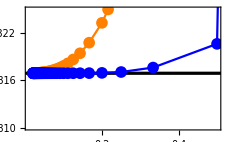

```mathematica
line=Plot[baselineVal,{x,0,50},PlotStyle->{Black,Thickness->0.01}];
ins1=ListPlot[dataCosAbs[[1;;50]],Frame->True,FrameStyle->Thickness[0.006],FrameTicksStyle->12,ImageSize->230,LabelStyle->Black,PlotStyle->{Orange,PointSize[0.02]},PlotRange->{{0.01,0.5},{5.881,5.8825}},Joined->True,PlotMarkers->{Automatic,12}];
ins2=ListPlot[dataLCTAbs[[1;;50]],Frame->True,FrameStyle->Thickness[0.006],FrameTicksStyle->12,ImageSize->230,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0.01,0.5},{5.8732,5.89}},Joined->True,PlotMarkers->{Automatic,12}];
convInset=Show[ins1,ins2,line]
```

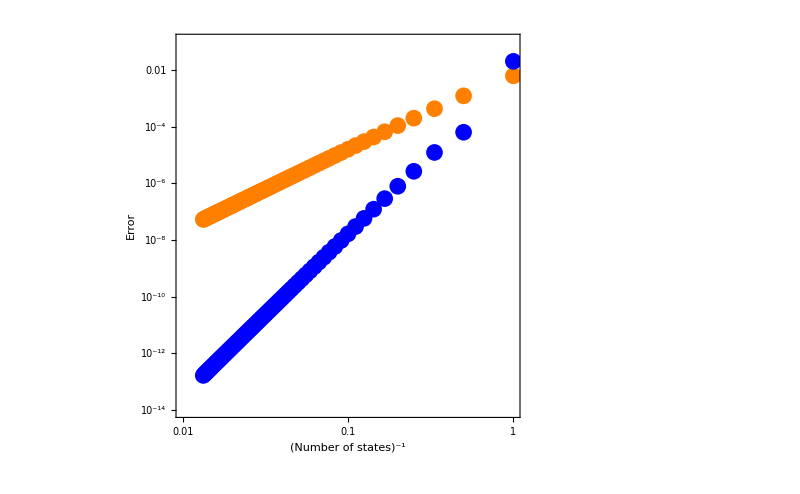

```mathematica
mainPlot1=ListLogLogPlot[dataCos[[1;;75]],Frame->True,FrameStyle->Thickness[0.0020],FrameLabel->{Style["(ℓ_max)^-1",FontFamily->"Times",FontSize->24],Style["Error",FontFamily->"Times",FontSize->24]},FrameTicksStyle->18,ImageSize->800,(*PlotLabel->Style["Δ_max = 80   2-parton",20],*)LabelStyle->{Black,FontFamily->"Times"},PlotStyle->{Orange,PointSize[0.015]},PlotRange->{{0.01,1},{ 10^-14,10^-1}},Epilog->{Inset[Style["Eigenvalue",FontFamily->"Times"],{4.7,.3},{0,0},FormatType->TraditionalForm,BaseStyle->20],Inset[convInset,Scaled[{.185,.82}]]},PlotLegends->Placed[SwatchLegend[{"Cosine Basis"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],Scaled[{0.88,.15}]]];
mainPlot2=ListLogLogPlot[dataLCT[[1;;75]],Frame->True,FrameStyle->Thickness[0.0020],FrameLabel->{Style["(ℓ_max)^-1",FontFamily->"Times",FontSize->24],Style["Error",FontFamily->"Times",FontSize->24]},FrameTicksStyle->18,ImageSize->700,(*PlotLabel->Style["Δ_max = 80   2-parton",20],*)LabelStyle->Black,PlotStyle->{Blue,PointSize[0.015]},PlotRange->{{0.01,.5},{10^-8,10^-2}},PlotLegends->Placed[SwatchLegend[{"LCT Basis"},LabelStyle->{FontFamily->"Times",20},LegendLayout->{"Row",5}],Scaled[{0.88,.15}]]];
finalPlot=Show[mainPlot1,mainPlot2,FrameLabel->{Style["(Number of states)^-1",FontFamily->"Times",FontSize->24],Style["Error",FontFamily->"Times",FontSize->24]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./LargeNConvergence.pdf",finalPlot];
```